```mathematica
Clear[xv,drdr,drdϕ,hr,hϕ,er,eϕ]
xv[r_,ϕ_]:=r{Cos[ϕ],Sin[ϕ]}
drdr[r_,ϕ_]:= D[xv[r,ϕ],r];
drdϕ[r_,ϕ_]:= D[xv[r,ϕ],ϕ];
hr[r_,ϕ_]= FullSimplify[Norm[drdr[r,ϕ]]//ComplexExpand,Assumptions->r>0];
hϕ[r_,ϕ_] = FullSimplify[Norm[drdϕ[r,ϕ]]//ComplexExpand,Assumptions->r>0];
er[r_,ϕ_]=drdr[r,ϕ]/hr[r,ϕ]
eϕ[r_,ϕ_]=drdϕ[r,ϕ]/hϕ[r,ϕ]
```

{Cos[ϕ],Sin[ϕ]}

{-Sin[ϕ],Cos[ϕ]}

```mathematica
Last[FullSimplify[Solve[{x,y}==xv[r,ϕ],{r,ϕ}],Assumptions->{r>0,ϕ>0}]]
```

{r→√(x^2+y^2),ϕ→ConditionalExpression[ArcTan[x,y]+2 π C[1], C[1]∈ℤ]}

```mathematica
Clear[repl]
repl[x_,y_]:={r->√(x^2+y^2),ϕ->ArcTan[x,y]};
```

```mathematica
Clear[A]
A[r_,ϕ_]=r^α eϕ[r,ϕ]
```

{-r^α Sin[ϕ],r^α Cos[ϕ]}

```mathematica
A[r,ϕ]/.repl[x,y]
```

{-y (x^2+y^2)^(-1/2+α/2),x (x^2+y^2)^(-1/2+α/2)}

```mathematica
StreamPlot[A[r,ϕ],{r,0,10},{ϕ,0,2π}];
Manipulate[StreamDensityPlot[(A[r-R,ϕ]/.repl[x,y])/.{α->-3},{x,-1,1},{y,-1,1}],{{R,0},-2,2}]
```

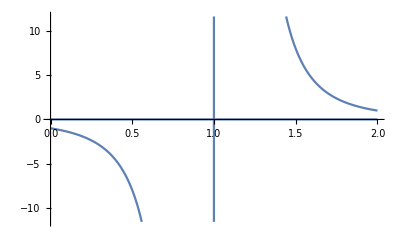

```mathematica
Plot[A[r-1,0]/.{α->-3},{r,0,2}]
```

```mathematica
Curl[(A[r-R,ϕ]/.repl[x,y]),{x,y}]//Simplify
```

((-R+√(x^2+y^2))^(-1+α) (-R+√(x^2+y^2) (1+α)))/(√(x^2+y^2))

```mathematica
Manipulate[Plot[(r^2)^(1/2 (-1+α)) (1+α),{r,0,10},PlotRange->{-1,1}0.0003],{α,-1,1}]
```